# 2 DEG Magneto - electric Properties

## Manipulate conductivity using dressing field intensity

#### Normalized conductivity function

```mathematica
σ[x_,n_,Λ0_,Λ1_] =(0.5*(n+1))/(0.0037*Λ0*Λ1)* (1/(1+((x-n-1)/(0.06*Λ0))^2))*(1/(1+((x-n)/(0.06*Λ1))^2));
I0 = List[1.0000,0.8660,0.8004,0.7578,0.7266,0.7021,0.6821,0.6653,0.6507,0.6380,0.6267];
I1 = List[0.8546,0.7037,0.6502,0.6114,0.5810,0.5584,0.5416,0.5280,0.5160,0.5050,0.4948];
I4 = List[0.6875,0.6345,0.5902,0.5528,0.5307,0.5118,0.4958,0.4840,0.4730,0.4629,0.4547];
I9= List[0.5936,0.5539,0.5333,0.5180,0.5006,0.4812,0.4685,0.4564,0.4469,0.4377,0.4305];
I16= List[0.5333,0.4998,0.4824,0.4706,0.4617,0.4543,0.4470,0.4379,0.4274,0.4194,0.4125];
I25= List[0.4899,0.4606,0.4454,0.4350,0.4272,0.4208,0.4155,0.4109,0.4068,0.4029,0.3984];
I49= List[0.4301,0.4061,0.3937,0.3852,0.3787,0.3735,0.3691,0.3654,0.3602,0.3591,0.3564];
```

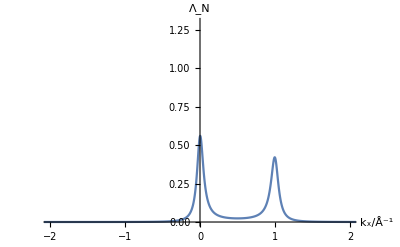

```mathematica
Plot[ σ[x,0,1.0,0.866],{x,-5,5},
PlotRange->{{-2,2},{0,1.3}},AxesLabel->{Style["  k_x/Å^-1",FontSize->20,FontColor->Black],Style["Λ_N",FontSize->20,FontColor->Black]},
AxesStyle->{Directive[Black,15],Directive[Black,15]},LabelStyle->Larger]
```

```mathematica
For[n=2;t0:=σ[x,0,Extract[I0,1],Extract[I0,2]],n<11,n++,
t0=t0 +σ[x,(n-1),Extract[I0,n],Extract[I0,n+1]]];
For[n=2;t1:=σ[x,0,Extract[I1,1],Extract[I1,2]],n<11,n++,
t1=t1 +σ[x,(n-1),Extract[I1,n],Extract[I1,n+1]]];
For[n=2;t4:=σ[x,0,Extract[I4,1],Extract[I4,2]],n<11,n++,
t4=t4 +σ[x,(n-1),Extract[I4,n],Extract[I4,n+1]]];
For[n=2;t9:=σ[x,0,Extract[I9,1],Extract[I9,2]],n<11,n++,
t9=t9+σ[x,(n-1),Extract[I9,n],Extract[I9,n+1]]];
For[n=2;t16:=σ[x,0,Extract[I16,1],Extract[I16,2]],n<11,n++,
t16=t16+σ[x,(n-1),Extract[I16,n],Extract[I16,n+1]]];
For[n=2;t25:=σ[x,0,Extract[I25,1],Extract[I25,2]],n<11,n++,
t25=t25+σ[x,(n-1),Extract[I25,n],Extract[I25,n+1]]];
For[n=2;t49:=σ[x,0,Extract[I49,1],Extract[I49,2]],n<11,n++,
t49=t49+σ[x,(n-1),Extract[I49,n],Extract[I49,n+1]]];
```

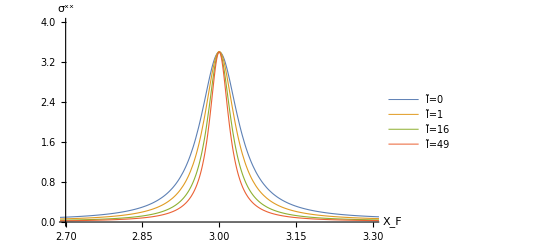

```mathematica
Plot[{t0,t1,t16,t49},{x,2.5,3.5}, 
PlotLegends->{"OverTilde[<I>]=0","OverTilde[<I>]=1","OverTilde[<I>]=16","OverTilde[<I>]=49"},
PlotRange->{{2.7,3.3},{0,4}},
PlotStyle->{Thickness[0.002]},
AxesLabel->{Style[" X_F",FontSize->20,FontColor->Black],Style["σ^xx",FontSize->20,FontColor->Black]},
AxesStyle->{Directive[Black,15],Directive[Black,15]},LabelStyle->Larger]
```

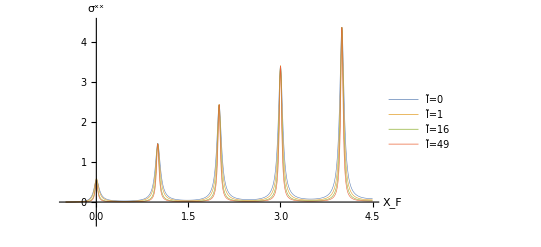

```mathematica
Plot[{t0,t1,t16,t49},{x,-0.5,4.5}, 
PlotLegends->{"OverTilde[<I>]=0","OverTilde[<I>]=1","OverTilde[<I>]=16","OverTilde[<I>]=49"},
PlotStyle->{Thickness[0.001]},
PlotRange->{-0.5,4.5},AxesLabel->{Style[" X_F",FontSize->20,FontColor->Black],Style["σ^xx",FontSize->20,FontColor->Black]},
AxesStyle->{Directive[Black,15],Directive[Black,15]},LabelStyle->Larger]
```

```mathematica
Export["s1.pdf",-Graphics-];
Export["s2.pdf",-Graphics-];
```